```mathematica
AddNode[g_,v1_,v2_,v3_]:=Block[{new=Max[VertexList[g]]+1},
Graph[EdgeAdd[g,{v1<->new,v2<->new,v3<->new}],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
]
```

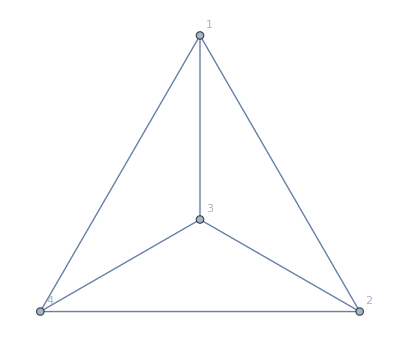

```mathematica
g1=AddNode[CompleteGraph[3],1,2,3]
```

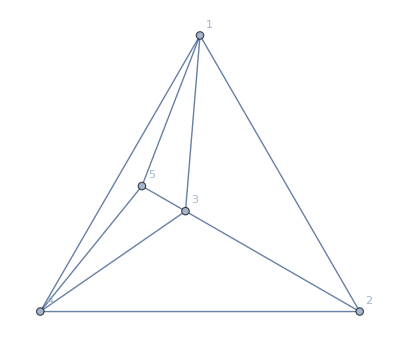

```mathematica
g2=AddNode[g1,1,4,3]
```

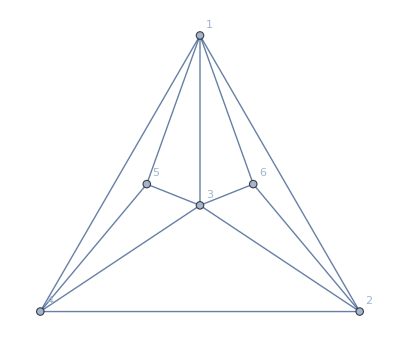

```mathematica
g3=AddNode[g2,1,2,3]
```

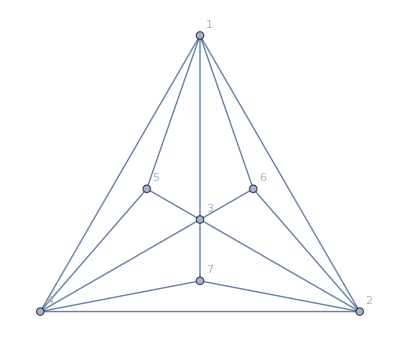

```mathematica
g4=AddNode[g3,4,2,3]
```

```mathematica
With[{g=g4},{
Graph[g,GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick"],
Sort[Map[VertexDegree[g,#]&,VertexList[g]]],
ChromaticPolynomial[Graph[CollectMPGEdges[g]],4]/24}]
```

{-Graphics-,{3,3,3,5,5,5,6},115/2}

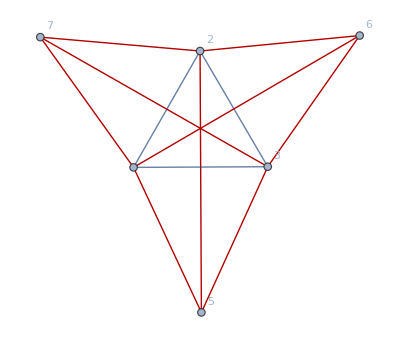

```mathematica
Graph[EdgeAdd[VertexContract[g4,{1,4}],2<->5],GraphLayout->"SpringEmbedding",GraphHighlight->CollectMPGEdges[EdgeAdd[VertexContract[g4,{1,4}],2<->5]]]
```



```mathematica
CompleteGraph[5]
```

```mathematica
ShowGraphSolutions[g_]:=Block[{},
FindFullFormula1234[g]->Monitor[Table[FindFullFormula1234[EdgeContract[g,e]],{e,CollectMPGEdges[g]}],e]
]
```

```mathematica
ShowGraphSolutions[Graph[JacobsThalGraph[4]]]
```

{v1x257x34x68,v17x26x34x58,v17x25x34x68,v16x27x34x58,v16x257x34x8,v168x2x34x57,v168x27x34x5,v18x26x34x57,v168x257x3x4,v18x257x34x6,v168x25x34x7,v168x257x34}→{{v17x34x5x68,v16x34x57x8,v1x34x57x68,v17x34x58x6,v16x34x58x7},{v168x2x4x57},{v1x257x4x68},{v1x257x3x68},{v168x2x3x57},{v17x2x34x68,v18x27x34x6,v1x27x34x68,v17x26x34x8,v18x26x34x7},{v1x26x34x57,v17x26x34x5,v17x25x34x6,v16x25x34x7,v16x2x34x57},{v16x257x3x4},{v168x27x3x4},{v168x27x3x4},{v1x27x34x58,v17x2x34x58,v17x25x34x8,v18x25x34x7,v18x27x34x5},{v18x257x3x4},{v18x257x3x4},{v1x26x34x58,v16x2x34x58,v16x25x34x8,v18x26x34x5,v18x25x34x6},{v168x25x3x4},{v168x25x3x4},{v1x26x34x57,v17x26x34x5,v17x25x34x6,v16x2x34x57,v16x25x34x7},{v16x257x3x4}}

```mathematica
FindRefinements[SymbolToSets[v168x25x3x4]]
```

{{{1,2,5,6,8},{3},{4}},{{1,3,6,8},{2,5},{4}},{{1,4,6,8},{2,5},{3}},{{1,6,8},{2,3,5},{4}},{{1,6,8},{2,4,5},{3}},{{1,6,8},{2,5},{3,4}}}

```mathematica
ShowGraphSolutions2[g_]:=Block[{all=Map[SymbolToSets[#]&,FindFullFormula1234[g]], fathers},
fathers=Monitor[Flatten[Table[Map[FindCoarser[SymbolToSets[#]]&,FindFullFormula1234[EdgeContract[g,e]]],{e,CollectMPGEdges[g]}],2]//DeleteDuplicates//Sort,e];
Table[
Table[
MemberQ[fathers,v]
,
{v,FindCoarser[s]}
]
,{s,all}];
Graph[FormulaGraphReverse2[Map[SetsToSymbol,Join[all,fathers]]],GraphHighlight->Map[SetsToSymbol,all]]
]
```

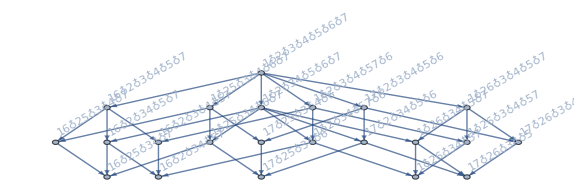
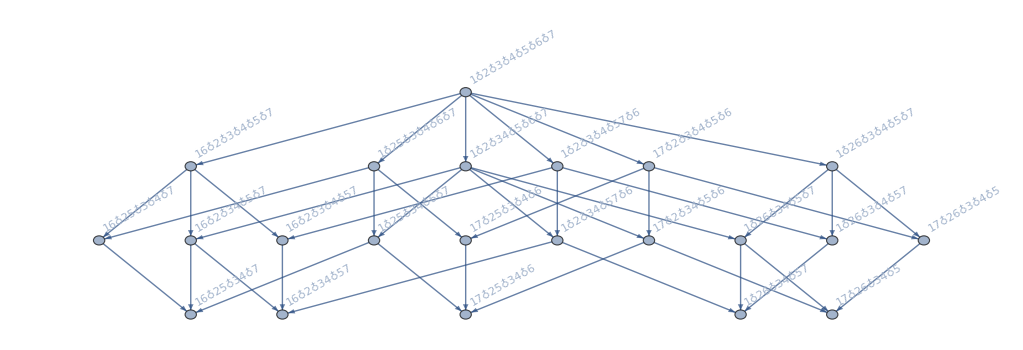

```mathematica
With[{g=JacobsThalGraph[3]},Table[Graph[FormulaGraphReverse2[FindFullFormula[g]],GraphHighlight->EdgeList[FormulaGraphReverse2[FindFullFormula[EdgeContract[g,e]]]]],{e,Take[EdgeList[g],2]}]]
```

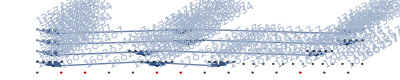

```mathematica
ShowGraphSolutions2[Graph[JacobsThalGraph[3]]]
```

```mathematica
FindFiner[SymbolToSets[v168x25x3x4]]
```

{{{1},{2,5},{3},{4},{6,8}},{{1,6},{2,5},{3},{4},{8}},{{1,8},{2,5},{3},{4},{6}},{{1,6,8},{2},{3},{4},{5}}}

```mathematica
ShowGraphSolutions3[g_]:=Block[{all=Map[SymbolToSets[#]&,FindFullFormula1234[g]], fathers},
fathers=Select[Monitor[Flatten[Table[Map[FindFiner[SymbolToSets[#]]&,FindFullFormula4[EdgeContract[g,e]]],{e,CollectMPGEdges[g]}],2]//DeleteDuplicates//Sort,e],Length[#]==5&];
Table[Fold[Or,Table[IsRefinement[a,f],{f,fathers}]],{a,all}]
]
```

```mathematica
ShowGraphSolutions3[JacobsThalGraph[2]]
```

{True,True,True,True}

```mathematica
ShowGraphSolutions4[g_]:=Block[{all=Map[SymbolToSets[#]&,FindFullFormula1234[g]], fathers},
Map[SetsToSymbol,Flatten[Map[FindFiner,all],1]]
]
```

```mathematica
With[{g=MinimalGraph[5]},
Block[{
all=FindFullFormula4[g], 
rest=DeleteDuplicates[Flatten[Table[Map[SymbolReplace[#,e]&,Flatten[FindFullFormula4[EdgeContract[g,e]]]],{e,EdgeList[g]}]]]
}
,
Print[rest];
rest=Map[SetsToSymbol,DeleteDuplicates[Flatten[Map[FindFiner[SymbolToSets[#]]&,rest],1]]];
Print[all];
Print[rest];
Map[If[MemberQ[all,#],Style[#,Red],If[MemberQ[rest,#],Style[#,Blue],#]]&,ShowGraphSolutions4[JacobsThalGraph[2]]]]
]
```

{v12x3x46x5,v12x36x4x5,v12x35x4x6,v13x2x46x5,v1x2x46x5,v14x2x36x5,v14x2x35x6,v1x24x36x5,v1x24x35x6,v1x2x346x5,v15x2x3x46,v15x2x36x4,v1x25x3x46,v1x25x36x4,v1x2x36x45,v16x2x35x4,v1x26x35x4,v1x2x356x4}

{v1x2x35x46}

{v1x2x3x46x5,v12x3x4x5x6,v1x2x36x4x5,v1x2x35x4x6,v13x2x4x5x6,v1x2x4x5x6,v14x2x3x5x6,v1x24x3x5x6,v1x2x34x5x6,v15x2x3x4x6,v1x25x3x4x6,v1x2x3x45x6,v16x2x3x4x5,v1x26x3x4x5,v1x2x3x4x56}

{v1x2x34x5x6,v1x25x3x4x6,v1x2x34x5x6,v16x2x3x4x5,v1x25x3x4x6,v16x2x3x4x5,v1x25x34x6,v16x2x34x5,v16x25x3x4}